# Interpolating Functions

## Introduction

This notebook explains how to use and operate on interpolating functions in Mathematica. These functions are either created by certain commands, like Interpolation, or else are returned by NDSolve as the solutions to differential equations. In both cases the functions are intended to predict continuous behavior from a discrete set of data points, and to behave as continuous functions with respect to most other Mathematica commands. There are, however, subtle differences between NDSolve interpolations and Interpolate interpolations, which are (this is Mathematica, after all) very frustrating to figure out. This notebook, then, is also intended to explain these differences.

## Plain Old Interpolation

The simplest way to creat interpolating functions in Mathematica is to use the command Interpolation. This command accepts as an argument an array of data points. The array may consist of either values or argument-value pairs (i.e., either {y1, y2, y3...} or {{x1, y1},{x2, y2}...}). Interpolation examines the array and predicts continuous behavior from it - in other words, it interpolates all values falling between those given in the array. It is very powerful and very robust. Here is an example.

Creating Interpolating Functions

First, make a table of sample data. For simplicity, use a sine function:

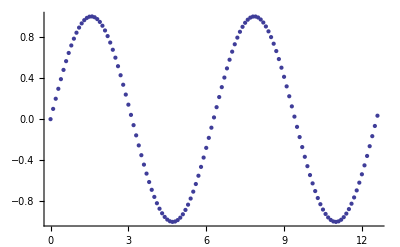

```mathematica
data = Table[{t,Sin[ t]},{t,0, 4Pi+.1, .1}];
ListPlot[data]
```

Now apply Interpolation to the data array:

InterpolatingFunction[{{0.,12.6}},<>]

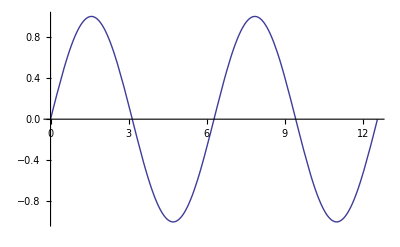

```mathematica
dataIF = Interpolation[data]
Plot[dataIF[t],{t,0,4Pi}]
```

Notice how, once dataIF is set equal to the output of Interpolation, dataIF behaves as a function - you can add a [t] to the end to evaluate it at specific points, or plot it. 
In fact, you can do almost anything to dataIF that you would do to an ordinary function. Examples:

```mathematica
FindMaximum[dataIF[t],{t,Pi/2}]
```

{0.999998,{t→1.57084}}

```mathematica
FindRoot[dataIF[t],{t,Pi}]
```

{t→3.14159}

However, if you wish to set the output of functions like FindMaximum or FindRoot equal to some variable, and then operate on that variable, you must be very careful. The output of FindMaximum or FindRoot is technically an array of rules. To get the actual value, you must apply the rule contained in the element of the array to some variable. Here's an example.

```mathematica
root = FindRoot[dataIF[t],{t,Pi}]
```

{t→3.14159}

Operating on root won't work:

```mathematica
value = dataIF[root]
```

{InterpolatingFunction[{{0.,12.6}},<>][t→3.14159]}

You must take the first (and only) element of the array that is actually returned by FindRoot, which is a rule, apply the rule to the given variable, and set the result equal to a different variable  (or the same one, if you don't mind overwriting it). Rules are essentially just Mathematica's way of specifying transformations. They always use the arrow notation, and can be applied to a variable or expression using the /. combination. Read /. as "such that" and read → as "goes to". For example:

```mathematica
arule = a -> (x+1);
a^2 /. arule
```

(1+x)^2

can be read as " a^2 such that a goes to x+1".

However, it is important to note that the variable used in the declaration of the rule must be present in the expression the rule is applied to. For example, the following code won't work:

```mathematica
arule = a -> (x+1);
b^2 /. arule
```

b^2

Extracting the output of FindRoot is very similar to the above procedure. Use the First command to get the element of the array, and apply this element (which is a rule) to some variable:

```mathematica
root
```

{t→3.14159}

```mathematica
First[root]
```

t→3.14159

```mathematica
troot = t /. First[root];
value = dataIF[troot]
```

-1.31243×10^-16

```mathematica
troot
```

3.14159

Note how now dataIF, or any function, will accept the variable troot as an argument, since it is no longer an array but an actual number.

Taking Derivatives

Taking derivatives of interpolating functions is quite straightforward. It requires using the Derivative command, which is more general than the usual command for symbolic expressions, D[]. The output is simply another interpolating function. Here's an example:

InterpolatingFunction[{{0.,12.6}},<>]

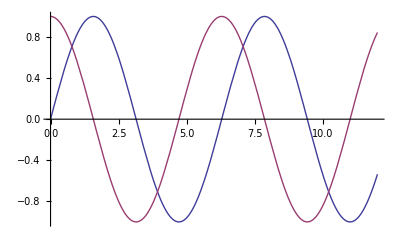

```mathematica
dataIFd = Derivative[1][dataIF]
Plot[{dataIF[t], dataIFd[t]},{t,0,12}]
```

Note that you do not need to specify an argument (i.e., no [t]) when applying Derivative to dataIF. The reasons are obscure and confusing, having to do with how function objects work in Mathematica. The [1] in brackets after Derivative just specifies how many times to take the derivative - 2 or 3 will give the 2nd or 3rd derivative, and so on.

Integrals

Unfortunately, you can't use the Integrate command to find an interpolating function approximating the symbolic integral of a given interpolating function, as you can with the Derivative command. However, you can find numerical integrals very easily. Here's an example:

```mathematica
definiteInt = Integrate[dataIF[t],{t,0,Pi}]
```

2.

If you don't mind a little bit of extra code, it's possible to manually create an interpolating function that approximates the symbolic integral, using the Table command. The resulting function isn't centered on the x-axis, which is a consequence of the arbitrary integration constant produced during indefinite integration, but the 'shape' of the function is pretty well approximated.

```mathematica
dataIFi = Interpolation[Table[{i,Integrate[dataIF[t],{t,0,i}]},{i,0,12,.1}]]
```

InterpolatingFunction[{{0.,12.}},<>]

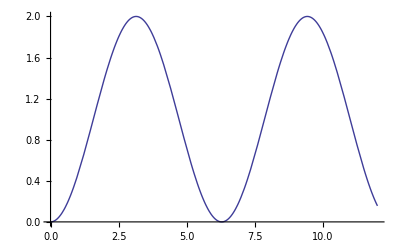

```mathematica
Plot[dataIFi[t],{t,0,12}]
```

Notes on Power

The Interpolation command is very powerful. This is illustrated below, with the same sine wave as used above, except with drastically reduced sampling. The first plot shows the sampled data points, of which there are only six. The second plot, of the interpolation function produced from these points, superimposed on the original sine wave, illustrates how close to the original function the interpolation is.

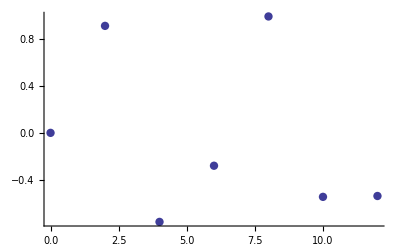

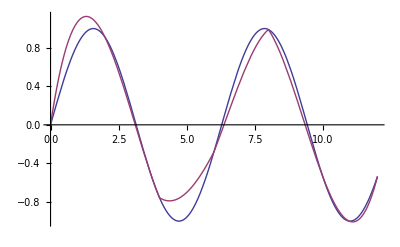

```mathematica
data2 = Table[{t,Sin[ t]},{t,0, 4Pi+.1, 2}];
ListPlot[data2,PlotStyle->{PointSize[.015]}]
Plot[{Sin[t],Interpolation[data2][t]},{t,0,12}]
```

## NDSolve Interpolating Functions

The other important use of interpolating functions in Mathematica is as the output of the NDSolve command. Essentially, NDSolve generates a list of solutions to the given differential equations in the form {t, x(t)}, where x(t) is the solution for some dynamical variable. NDSolve then automatically applies Mathematica's Interpolation command to this list, and outputs the resulting interpolating function. Here's a simple example.

Creating Interpolating Functions

```mathematica
sol = NDSolve[{x''[t] - .2x'[t] + 5x[t] ==0, y'[t] == x[t]+.5,x[0] ==1, z'[t] == .5,x'[0] == 10 ,y[0] ==0,z[0] ==0},{x,y,z},{t,0,100}]
```

{{x→InterpolatingFunction[{{0.,100.}},<>],y→InterpolatingFunction[{{0.,100.}},<>],z→InterpolatingFunction[{{0.,100.}},<>]}}

There are several important things to note about the form of NDSolve's output. First, it is a nested array - there is the top-level array, the element of which is a two element array containing the interpolating functions. Second, the interpolating functions are given in terms of rules, so that you must use the /. notation to 'access' the interpolating functions. First gives the first element in the expression. For example the first element in this list is:

```mathematica
First[{a,b,c}]
```

a

while the first element in this list is a list :

```mathematica
First[{{a,b},{d,c}}]
```

{a,b}

```mathematica
First[{{a,b,c}}]
```

and the only element in this list is a list containing three elements :

{a,b,c}

```mathematica
First[sol]
```

{x→InterpolatingFunction[{{0.,100.}},<>],y→InterpolatingFunction[{{0.,100.}},<>],z→InterpolatingFunction[{{0.,100.}},<>]}

First[sol] is a list of three rules

```mathematica
First[First[sol]]
```

x→InterpolatingFunction[{{0.,100.}},<>]

First[First[sol]] is the first rule, or equivalently

```mathematica
Part[First[sol],1]
```

x→InterpolatingFunction[{{0.,100.}},<>]

```mathematica
Part[First[sol],2]
```

y→InterpolatingFunction[{{0.,100.}},<>]

```mathematica
y[t] /.sol
```

{InterpolatingFunction[{{0.,100.}},<>][t]}

y[t] /. sol is a list of one element, the function y[t]

```mathematica
y[t] /.First[sol]
```

InterpolatingFunction[{{0.,100.}},<>][t]

y[t] /. First[sol] is the function y[t]

```mathematica
y[10] /.First[sol]
```

11.4748

```mathematica
y[10] /.sol
```

{11.4748}

```mathematica
First[y[10] /.sol]
```

11.4748

First [y[t] /. sol] is also the function y[t]

The command FindRoot can be used exactly as they are with regular interpolating functions:

```mathematica
FindRoot[x[t] ==0 /. sol,{t,1}]
```

{t→1.30702}

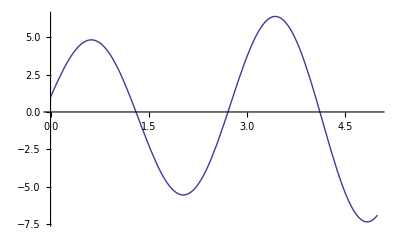

```mathematica
Plot[x[t]/.sol,{t,0,5}]
```

FindMaximum works too:

```mathematica
FindMaximum[x[t]/.sol,{t,3}]
```

{6.40005,{t→3.43661}}

Creating Plots

Plotting the interpolating functions produced by NDSolve is not as straightforward as plotting regular interpolating functions. The difficulties again arise from one-element arrays and quirks in the plotting functions. 
Plotting one variable is, however, easy:

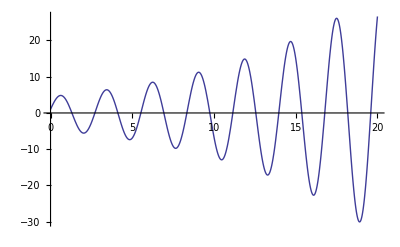

```mathematica
Plot[x[t]/.sol,{t,0,20}]
```

To plot two variables on the same graph:

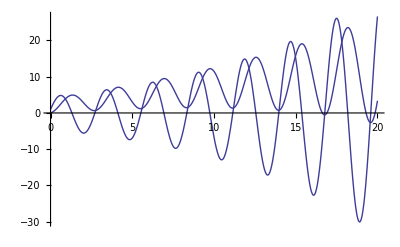

```mathematica
Plot[{x[t],y[t]} /. sol,{t,0, 20}]
```

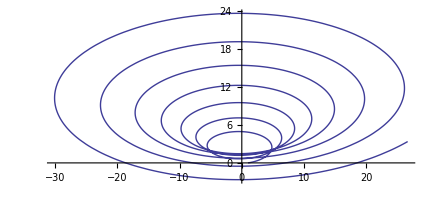

```mathematica
ParametricPlot[{x[t],y[t]} /. sol,{t,0,20}]
```

```mathematica
ParametricPlot3D[{x[t],y[t],z[t]} /. sol, {t,0,20}]
```

-Graphics3D-

Getting actual data from Interpolating Functions

There are some commands in Mathematica that need lists or arrays of data, and not interpolating functions. An important example are the commands for doing Fourier transforms. While Mathematica does have commands for performing Fourier transforms on analytic expressions, they do not work with interpolating functions. It is therefore necessary to create a list or array of data from an interpolating function, and use the discrete Fourier transform command on this data. This is straightforward to do, using the Table command. The only trick is to once again use the First command. Here is an example, using the interpolating functions used above.

```mathematica
data = Table[First[x[i] /. sol],{i,0,5,.1}]
```

{1.,1.97661,2.87354,3.64406,4.24688,4.64829,4.82403,4.7607,4.45667,3.92235,3.17997,2.26266,1.21302,0.0811749,-1.07762,-2.20563,-3.24549,-4.14314,-4.85055,-5.32829,-5.54772,-5.49256,-5.16005,-4.5613,-3.72106,-2.6767,-1.47662,-0.178038,1.15573,2.45833,3.66359,4.70896,5.53861,6.10646,6.37868,6.33558,5.97299,5.30266,4.3521,3.16347,1.79171,0.302139,-1.23272,-2.73659,-4.13321,-5.35017,-6.32264,-6.99676,-7.33261,-7.30647,-6.91233}

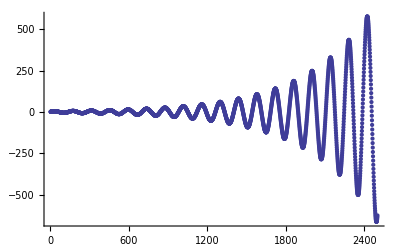

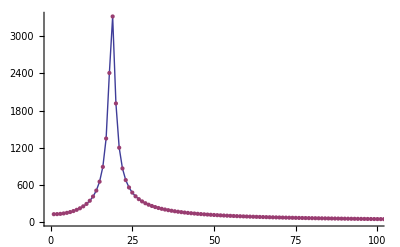

```mathematica
data = Table[First[x[i] /. sol],{i,0,50,.02}];
dataF = Fourier[data];
ListPlot[data,PlotRange->All]
ListPlot[{Abs[dataF],Abs[dataF]},Joined->{True,False},PlotRange->{{0,100},All}]
```